```mathematica
Integrate[Integrate[r(-16r^2Sin[t]Cos[t]+2r^2Sin[t]^2+3Cos[t]),{r,0,2}],{t,0,2Pi}]
```

8 π

```mathematica
Integrate[-Sin[t]^2,{t,0,2Pi}]
```

-π

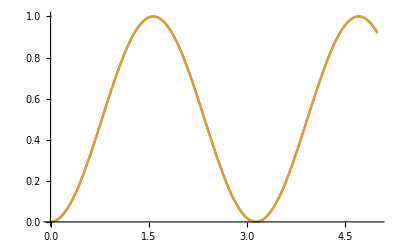

```mathematica
Plot[{Sin[x]^2,1/2(1-Cos[2x])},{x,0,5}]
```

```mathematica
F={y,z,x}
```

{y,z,x}

```mathematica
Curl[F,{x,y,z}]
```

{-1,-1,-1}

```mathematica
S={Cos[t] Sin[p],Sin[t]Sin[p],Cos[p]};
rt=D[S,t]
rp=D[S,p]
```

{-Sin[p] Sin[t],Cos[t] Sin[p],0}

{Cos[p] Cos[t],Cos[p] Sin[t],-Sin[p]}

```mathematica
cross=Assuming[{t,p}∈Reals,FullSimplify[Cross[rt,rp]]]
```

{-Cos[t] Sin[p]^2,-Sin[p]^2 Sin[t],-Cos[p] Sin[p]}

```mathematica
int=Assuming[{t,p}∈Reals,FullSimplify[Dot[{-1,-1,-1},{-Cos[t] Sin[p]^2,-Sin[p]^2 Sin[t],Cos[p] Sin[p]}]]]
```

Sin[p] (-Cos[p]+Sin[p] (Cos[t]+Sin[t]))

```mathematica
Integrate[Integrate[int,{t,0,2Pi}],{p,0,Pi/2}]
```

-π

```mathematica
ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]},{u,0,2Pi},{v,0,Pi/2}]
```

-Graphics3D-

```mathematica
int
```

Sin[p] (-Cos[p]+Sin[p] (Cos[t]+Sin[t]))

```mathematica
Expand[int]/.{t->u,p->v}
```

-Cos[v] Sin[v]+Cos[u] Sin[v]^2+Sin[u] Sin[v]^2

```mathematica
Assuming[{u,v}∈Reals,FullSimplify[Cross[{Cos[v],Sin[v],-2u},{-u Sin[v],u Cos[v],0}]]]
```

{2 u^2 Cos[v],2 u^2 Sin[v],u}

```mathematica
Dot[%,{u^2 Cos[v]^2,u^2 Sin[v]Cos[v],4-u^2}]
```

u (4-u^2)+2 u^4 Cos[v]^3+2 u^4 Cos[v] Sin[v]^2

```mathematica
Integrate[%,{u,0,2}]
```

4+(64 Cos[v]^3)/5+64/5 Cos[v] Sin[v]^2

```mathematica
Integrate[(64 Cos[v]^3)/5,v]+Integrate[64/5 Cos[v] Sin[v]^2,v]//FullSimplify
```

(64 Sin[v])/5

```mathematica
Integrate[4+(64 Cos[v]^3)/5+64/5 Cos[v] Sin[v]^2,{v,0,2Pi}]
```

8 π

```mathematica
Integrate[Integrate[{x y,3x^2,x^2 Exp[y]}.{-Exp[y],-x Exp[y],1},{x,0,1}],{y,0,1}]
```

1/12 (-1-5 ⅇ)

```mathematica
G={z,x,y};
r={Cos[t],Sin[t],0};
rprime=D[r,t]

Gr=G/.{x->r[[1]],y->r[[2]],z->r[[3]]}
Gr.rprime
Integrate[%,{t,0,2Pi}]
```

{-Sin[t],Cos[t],0}

{0,Cos[t],Sin[t]}

Cos[t]^2

π

```mathematica
Integrate[Cos[x](1-Sin[x]^2),x]
```

(3 Sin[x])/4+1/12 Sin[3 x]

```mathematica
F2={x,y,z};
r2={u Cos[v],u Sin[v], 4-u^2};
r2u=D[r2,u];
r2v=D[r2,v];
r2prime=Cross[r2u,r2v]

Fr = F2/.{x->r2[[1]],y->r2[[2]],z->r2[[3]]}
Fr.r2prime
%//FullSimplify
```

{2 u^2 Cos[v],2 u^2 Sin[v],u Cos[v]^2+u Sin[v]^2}

{u Cos[v],u Sin[v],4-u^2}

2 u^3 Cos[v]^2+2 u^3 Sin[v]^2+(4-u^2) (u Cos[v]^2+u Sin[v]^2)

u (4+u^2)

```mathematica
Integrate[Integrate[%,{u,0,2}],{v,0,2Pi}]
```

24 π

```mathematica
Div[F2,{x,y,z}]
```

3

```mathematica
ClearAll[r,z,t]
Integrate[Integrate[Integrate[%%*r,{z,0,4-r^2}],{r,0,2}],{t,0,2Pi}]
```

24 π

```mathematica
Curl[{1,Sin[z],y Cos[z]},{x,y,z}]
```

{0,0,0}

```mathematica
vec={1+3x^2,Sin[z],y Cos[z]};
Curl[vec,{x,y,z}]

Integrate[vec[[1]],x]+g[y,z]
Integrate[vec[[2]],y]+h[x,z]
Integrate[vec[[3]],z]+k[x,y]
```

{0,0,0}

x+x^3+g[y,z]

h[x,z]+y Sin[z]

k[x,y]+y Sin[z]

```mathematica
Grad[x^2+x^3+y Sin[z]+C[1],{x,y,z}]===vec
```

True

```mathematica
func=2x z+ y+ x y Exp[z]
grad=Grad[func,{x,y,z}]

f1=Expand[Integrate[grad[[1]],x]]+g[y,z]
f2=Expand[Integrate[grad[[2]],y]]+h[x,z]
f3=Expand[Integrate[grad[[3]],z]]+k[x,y]
```

y+ⅇ^z x y+2 x z

{ⅇ^z y+2 z,1+ⅇ^z x,2 x+ⅇ^z x y}

ⅇ^z x y+2 x z+g[y,z]

y+ⅇ^z x y+h[x,z]

ⅇ^z x y+2 x z+k[x,y]

```mathematica
D[f1,y]/.{Derivative[1,0][g][y,z]->g_y[y,z]}
Reduce[%==grad[[2]]]
```

ⅇ^z x+g_y[y,z]

g_y[y,z]==1

```mathematica
f12=Expand[Integrate[grad[[1]],x]]+y+h[z]

D[f12,z]
Reduce[%==grad[[3]]]
```

y+ⅇ^z x y+2 x z+h[z]

2 x+ⅇ^z x y+h'[z]

h'[z]==0

```mathematica
f13=Expand[Integrate[grad[[1]],x]]+y+C[1]
```

y+ⅇ^z x y+2 x z+C[1]

```mathematica
Integrate[t Cos[t] Exp[t],t]//Expand
```

1/2 ⅇ^t t Cos[t]-1/2 ⅇ^t Sin[t]+1/2 ⅇ^t t Sin[t]

```mathematica
grad
```

{ⅇ^z y+2 z,1+ⅇ^z x,2 x+ⅇ^z x y}

```mathematica
r={Sin[t],t^2,t};
(*ParametricPlot3D[r,{t,0,5}]*)

rprime=D[r,t]

grad/.{x->r[[1]],y->r[[2]],z->r[[3]]}

Dot[rprime,%]//Expand

Expand[Integrate[%,{t,0,5}]]

pt1=r/.{t->0};
pt2=r/.{t->5};
(func/.{x->pt2[[1]],y->pt2[[2]],z->pt2[[3]]})-(func/.{x->pt1[[1]],y->pt1[[2]],z->pt1[[3]]})
```

{Cos[t],2 t,1}

{2 t+ⅇ^t t^2,1+ⅇ^t Sin[t],2 Sin[t]+ⅇ^t t^2 Sin[t]}

2 t+2 t Cos[t]+ⅇ^t t^2 Cos[t]+2 Sin[t]+2 ⅇ^t t Sin[t]+ⅇ^t t^2 Sin[t]

25+10 Sin[5]+25 ⅇ^5 Sin[5]

25+10 Sin[5]+25 ⅇ^5 Sin[5]

```mathematica
n=10;
r3={(4+Sin[n t])Cos[t],(4+Sin[n t])Sin[t],Cos[n t]}
ParametricPlot3D[r3,{t,0,2Pi},Boxed->False,Axes->None,PlotStyle->{Bold,Red}]

gradr3=grad/.{x->r3[[1]],y->r3[[2]],z->r3[[3]]}
r3prime=D[r3,t]

Dot[r3prime,gradr3]//Expand

NIntegrate[%,{t,0,2 Pi},WorkingPrecision->15]
```

{Cos[t] (4+Sin[10 t]),Sin[t] (4+Sin[10 t]),Cos[10 t]}

-Graphics3D-

{2 Cos[10 t]+ⅇ^Cos[10 t] Sin[t] (4+Sin[10 t]),1+ⅇ^Cos[10 t] Cos[t] (4+Sin[10 t]),2 Cos[t] (4+Sin[10 t])+ⅇ^Cos[10 t] Cos[t] Sin[t] (4+Sin[10 t])^2}

{10 Cos[t] Cos[10 t]-Sin[t] (4+Sin[10 t]),10 Cos[10 t] Sin[t]+Cos[t] (4+Sin[10 t]),-10 Sin[10 t]}

4 Cos[t]+16 ⅇ^Cos[10 t] Cos[t]^2+20 Cos[t] Cos[10 t]^2+2 Cos[10 t] Sin[t]+80 ⅇ^Cos[10 t] Cos[t] Cos[10 t] Sin[t]-16 ⅇ^Cos[10 t] Sin[t]^2-79 Cos[t] Sin[10 t]+8 ⅇ^Cos[10 t] Cos[t]^2 Sin[10 t]-160 ⅇ^Cos[10 t] Cos[t] Sin[t] Sin[10 t]-2 Cos[10 t] Sin[t] Sin[10 t]+20 ⅇ^Cos[10 t] Cos[t] Cos[10 t] Sin[t] Sin[10 t]-8 ⅇ^Cos[10 t] Sin[t]^2 Sin[10 t]-20 Cos[t] Sin[10 t]^2+ⅇ^Cos[10 t] Cos[t]^2 Sin[10 t]^2-80 ⅇ^Cos[10 t] Cos[t] Sin[t] Sin[10 t]^2-ⅇ^Cos[10 t] Sin[t]^2 Sin[10 t]^2-10 ⅇ^Cos[10 t] Cos[t] Sin[t] Sin[10 t]^3

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.63803835675298423227101537582133661297029070097201239970688434856}. NIntegrate obtained -6.4312586065286999736408960838475697718755033379900064359232771715×10^-20 and 5.1469332335787070011189670952442918662868611443443518048720292633×10^-15 for the integral and error estimates.

-6.4312586065287×10^-20

```mathematica
c=ParametricPlot3D[r3,{t,0,2Pi},Boxed->False,Axes->None,PlotStyle->{Bold,Red},MaxRecursion->15,PlotPoints->30000]

Show[{
Graphics3D[{
yaxis=Arrow[{{-5,0,0},{5,0,0}}],
xaxis=Arrow[{{0,5,0},{0,-5,0}}],
zaxis=Arrow[{{0,0,-4},{0,0,4}}]
},
	Boxed->False
],
c
}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Grad[x y z-x y + y z - x z + z^2,{x,y,z}]
```

{-y-z+y z,-x+z+x z,-x+y+x y+2 z}

```mathematica
?Grad
```

Grad[f,{x_1,…,x_n}] gives the gradient (∂f/∂x_1,…,∂f/∂x_n).
Grad[f,{x_1,…,x_n},chart] gives the gradient in the coordinates chart.

```mathematica
ClearAll[x,y]

varx=3Cos[t];
vary=3Sin[t];

xp=D[varx,t];
yp=D[vary,t];

P=y;
Q = x^2 y;

Integrate[vary xp + (varx)^2 vary yp,{t,0,Pi/2}]
Integrate[D[Q,x]-D[P,y],{x,y}∈Disk[{0,0},3,{0,Pi/2}]]
```

-9/4 (-9+π)

-9/4 (-9+π)

```mathematica
2.325/3
```

```mathematica
0.775
2.9875/3
```

0.775

0.995833

```mathematica
?Disk
```

Disk[{x,y},r] represents a disk of radius r centered at {x,y}.
Disk[{x,y}] gives a disk of radius 1. 
Disk[{x,y},{r_x,r_y}] gives an axis-aligned elliptical disk with semiaxes lengths r_x and r_y.
Disk[{x,y},…,{θ_1,θ_2}] gives a sector of a disk from angle θ_1 to θ_2.

```mathematica
Integrate[Integrate[1-x-y,{y,0,1-x}],{x,0,1}]
```

1/6

```mathematica
Integrate[Integrate[Integrate[1,{x,0,1-y-z}],{z,0,1-y}],{y,0,1}]
```

1/6